```mathematica
ClearAll["Global`*"];
eqns={a==1/6(1+pe)(3/2(1+pn)-1/2(1-qn)),
b==1/6(1+pe)(1-qn),
c==1/6(1+pe)(3/2(1-pn)-1/2(1-qn)),
d==1/6(1-pe)(3/2(1+pn)-1/2(1-qn)),
e==1/6(1-pe)(1-qn),
f==1/6(1-pe)(3/2(1-pn)-1/2(1-qn))}//Simplify
```

{12 a==(1+pe) (2+3 pn+qn),6 b+qn+pe qn==1+pe,12 c+(1+pe) (-2+3 pn-qn)==0,12 d+(-1+pe) (2+3 pn+qn)==0,6 e+pe+qn==1+pe qn,12 f==(-1+pe) (-2+3 pn-qn)}

```mathematica
(* Reproduces the equation set above, which means this is correct *)
Solve[{pe==a+b+c-d-e-f,
pn==a+d-c-f,
qn==a+d+c+f-2b-2e,
a+b+c+d+e+f==1,
a/d==b/e==c/f},
{a,b,c,d,e,f}]//Simplify
```

{{a→1/12 (1+pe) (2+3 pn+qn),b→-1/6 (1+pe) (-1+qn),c→-1/12 (1+pe) (-2+3 pn-qn),d→-1/12 (-1+pe) (2+3 pn+qn),e→1/6 (-1+pe) (-1+qn),f→1/12 (-1+pe) (-2+3 pn-qn)}}

{2 ω1+(4+β) ω1 pe[t]+β ω1 pn[t]+pe'[t]==2 ω1,cc θ ω1+cc β ω1 pe[t]+cc (β+2 (1+θ)) ω1 pn[t]+pn'[t]==(2+cc θ) ω1,pe[0]==-1,pn[0]==0}

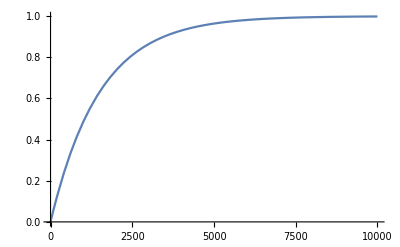

```mathematica
(* The JiZhi spin 1/2 case fully derived *)
ClearAll["Global`*"];
(*r=0;
σ=0;*)
(*t1e=0.03;
t1n=25*60;*)
physicalTimes={t1e->0.03,t1n->25*60};
(*ω1=1/t1e;
θ=t1e/(cc t1n);*)
a=1/4(1+pe[t])(1+pn[t]);
b=1/4(1+pe[t])(1-pn[t]);
c=1/4(1-pe[t])(1+pn[t]);
d=1/4(1-pe[t])(1-pn[t]);
aDot=-(β(a-d)+σ(a-r d)+θ(r a-b)+a-r c)ω1;
bDot=-(σ(b-r c)+θ(b-r a)+b-r d)ω1;
cDot=-(σ(r c-b)+θ(r c-d)+r c-a)ω1;
dDot=-(β(d-a)+σ(r d-a)+θ(d-r c)+r d-b)ω1;
pnDot=cc(aDot+cDot-bDot-dDot)+(1+r)ϕ ω1;
peDot=aDot+bDot-cDot-dDot;
pnDot//FullSimplify;
peDot//FullSimplify;
eqns={pe'[t]==peDot,pn'[t]==pnDot,pe[0]==-1,pn[0]==0};
sol=ParametricNDSolve[eqns,{pn,pe},{t,0,10000},{β,cc,θ,σ,r,ϕ}];
(*solExact=DSolve[{pe'[t]==peDot,pn'[t]==pnDot,pe[0]==-1,pn[0]==0},{pn,pe},t]*)
Simplify[eqns]/.{r->1,σ->1,ϕ->1}
(*Manipulate[Plot[{pn[beta,cee,2*^-5/cee,0,0,phi][t]/.sol,pe[beta,cee,2*^-5/cee,0,0,phi][t]/.sol},{t,0,2000},PlotRange->{{0,2000},{-1,1}},ImageSize->Large,PlotLegends->{"P_n","P_e"}],
{beta,0,5},{cee,0.1*^-4,10*^-4},{phi,0,1*^-4}]*)
sol2=DSolve[Evaluate[Simplify[eqns]/.{r->0,σ->0,ϕ->0}],{pn,pe},t];
(*Manipulate[Plot[pn[t]/.sol2/.{β->beta,cc->cee},{t,0,2000}],{beta,0,5},{cee,0.1*^-4,10*^-4}]*)
Plot[pn[t]/.sol2/.{β->0,cc->1*^-4,ω1->33.3,θ->0.2}/.physicalTimes,{t,0,10000},PlotRange->Full]
```

```mathematica
(* The spin 1 case *)
ClearAll["Global`*"];
r=0;
σ=0;
physicalTimes={t1e->0.03,t1n->25*60};
ω1=1/t1e;
θ=(2t1e)/(t1n con);
a=1/6(1+pe[t])(3/2(1+pn[t])-1/2(1-qn[t]));
b=1/6(1+pe[t])(1-qn[t]);
c=1/6(1+pe[t])(3/2(1-pn[t])-1/2(1-qn[t]));
d=1/6(1-pe[t])(3/2(1+pn[t])-1/2(1-qn[t]));
e=1/6(1-pe[t])(1-qn[t]);
f=1/6(1-pe[t])(3/2(1-pn[t])-1/2(1-qn[t]));
aDot=-((a-r d)+θ(r a-b)+β(a-e)+σ(a-re))ω1;
bDot=-((b-r e)+θ(r b-c)+θ(b-r a)+β(b-f)+σ(b-r f)+α(b-d)+σ(b-r d))ω1;
cDot=-((c-r f)+θ(c-r b)+α(c-e)+σ(c-r e))ω1;
dDot=-((r d-a)+θ(r d-e)+α(d-b)+σ(r d-b))ω1;
eDot=-((r e-b)+θ(r e-f)+θ(e-r d)+β(e-a)+σ(r e-a)+α(e-c)+σ(r e-c))ω1;
fDot=-((r f-c)+θ(f-r e)+β(f-b)+σ(r f-b))ω1;
eqns={pe'[t]==aDot+bDot+cDot-dDot-eDot-fDot,
pn'[t]==con(aDot+dDot-cDot-fDot),
qn'[t]==con(aDot+dDot+cDot+fDot-2bDot-2eDot),
pe[0]==-1,pn[0]==0,qn[0]==0};
sol=ParametricNDSolve[eqns,{pe,pn,qn},{t,0,2000},{t1e,t1n,con,α,β}]
Manipulate[Plot[{pe[t1e,t1n,con,α,β][t]/.physicalTimes/.sol,
pn[t1e,t1n,con,α,β][t]/.physicalTimes/.sol,
qn[t1e,t1n,con,α,β][t]/.physicalTimes/.sol},
{t,0,2000},PlotRange->{{0,2000},{-1,1}},ImageSize->Large,PlotLegends->{"P_e","P_n","Q_n"}],
{con,0.1*^-4,10*^-4},{α,0,5},{β,0,5}]
```

{pe→ParametricFunction[<>],pn→ParametricFunction[<>],qn→ParametricFunction[<>]}

ReplaceAll::reps: {physicalTimes} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {physicalTimes} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {physicalTimes} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {physicalTimes} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

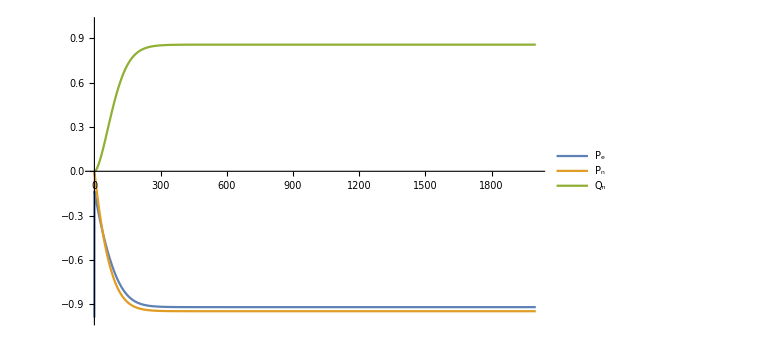

```mathematica
Plot[{pe[t1e,t1n,con,α,β][t]/.physicalTimes/.sol/.{con->10*^-4,α->5,β->0},
pn[t1e,t1n,con,α,β][t]/.physicalTimes/.sol/.{con->10*^-4,α->5,β->0},
qn[t1e,t1n,con,α,β][t]/.physicalTimes/.sol/.{con->10*^-4,α->5,β->0}},
{t,0,2000},PlotRange->{{0,2000},{-1,1}},ImageSize->Large,PlotLegends->{"P_e","P_n","Q_n"}]
```

```mathematica
Simplify[pnDot]
```

-ω1 (-cc θ+cc r θ-ϕ-r ϕ+cc (β+(1+r) (θ+σ)) pn[t]+cc pe[t] (β+(σ-r σ) pn[t]))